# Real-time simulation

This notebook introduces quantum simulation, and explores simulating the real-time dynamics of a spin-ring Ising system. We demonstrate classical analytic and numerical treatments, then study Trotterisation in the absence and presence of decoherence.

Contents:
    •  Analytic
    • Numerical
    • Trotterisation
        • Pure
        • Noisy

Tyson Jones, 2024
Department of Materials, University of Oxford
tyson.jones.input@gmail.com

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

## Analytic

In quantum simulation, we are interested in studying the properties of a time-dependent state ψ(t) as it evolves according to the physics of some Hamiltonian  Ĥ. Consider this arbitrary 3-qubit Hamiltonian specified in the Pauli basis:

```mathematica
nQb = 3;
h = Subscript[X, 0] Subscript[Y, 1] + 2 Subscript[Y, 2] Subscript[Z, 0]  - 3 Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2];
```

```mathematica
hMatr = CalcPauliExpressionMatrix[h]
```

SparseArray[…]

We’ll study the evolution of ψ(t) from initial state  ψ(0)=0  initial state.

```mathematica
ψ0 = UnitVector[2^nQb, 1]
```

{1,0,0,0,0,0,0,0}

One way to obtain the future states ψ(t) is to numerically solve the Schrödinger equation:
        ⅈ d/dt ψ(t)  = Ĥ ψ(0)

```mathematica
NDSolve[{ⅈ ψ'[t] == hMatr . ψ[t], ψ[0] == ψ0}, ψ, {t,0,4}];
ψ = %[[1,1,2]]
```

InterpolatingFunction[…]

```mathematica
ψ[0] // Chop
```

{1.,0,0,0,0,0,0,0}

```mathematica
ψ[.3] // Chop
```

{0.444122+0.700796 ⅈ,0,0,0.170249+0.216967 ⅈ,0.483035,0,0,0.-0.0475127 ⅈ}

We could instead obtain an analytic expression for ψ(t) = Û(t) ψ(0)  by symbolically constructing the unitary time evolution operator Û(t) = ⅇ^(-ⅈ t Ĥ)

```mathematica
u[t_] = MatrixExp[-ⅈ t CalcPauliExpressionMatrix[h]];
```

```mathematica
MatrixForm @ u[t]
```

(1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5)) | 0 | 0 | ⅈ (-1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t])+Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5) | -Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(2 √5) | 0 | 0 | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5))
0 | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (-Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5)) | ⅈ (1/2 Cos[2 √2 t]-1/2 Cos[2 √5 t])+Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5) | 0 | 0 | Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5) | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | 0
0 | ⅈ (-1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t])-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5) | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (-Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5)) | 0 | 0 | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | -Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(2 √5) | 0
ⅈ (1/2 Cos[2 √2 t]-1/2 Cos[2 √5 t])-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5) | 0 | 0 | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5)) | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | 0 | 0 | Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)
Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5) | 0 | 0 | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (-Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5)) | 0 | 0 | ⅈ (1/2 Cos[2 √2 t]-1/2 Cos[2 √5 t])+Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5)
0 | -Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(2 √5) | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | 0 | 0 | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5)) | ⅈ (-1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t])+Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5) | 0
0 | ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5) | 0 | 0 | ⅈ (1/2 Cos[2 √2 t]-1/2 Cos[2 √5 t])-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5) | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5)) | 0
ⅈ (-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(2 √5)) | 0 | 0 | -Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(2 √5) | ⅈ (-1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t])-Sin[2 √2 t]/(2 √2)+Sin[2 √5 t]/(√5) | 0 | 0 | 1/2 Cos[2 √2 t]+1/2 Cos[2 √5 t]+ⅈ (-Sin[2 √2 t]/(2 √2)-Sin[2 √5 t]/(√5)))

We can then obtain analytic expressions for the Z-basis amplitudes of ψ(t) as functions of t

```mathematica
Clear[ψ]
ψ[t] = u[t] . ψ0 // Simplify
```

{1/20 (10 Cos[2 √2 t]+10 Cos[2 √5 t]+5 ⅈ √2 Sin[2 √2 t]+4 ⅈ √5 Sin[2 √5 t]),0,0,1/20 (10 ⅈ Cos[2 √2 t]-10 ⅈ Cos[2 √5 t]-5 √2 Sin[2 √2 t]+4 √5 Sin[2 √5 t]),1/20 (5 √2 Sin[2 √2 t]+2 √5 Sin[2 √5 t]),0,0,-1/20 ⅈ (5 √2 Sin[2 √2 t]-2 √5 Sin[2 √5 t])}

Here’s how the probability of the basis states, with amplitudes α_i, evolve from δ_(i,0)

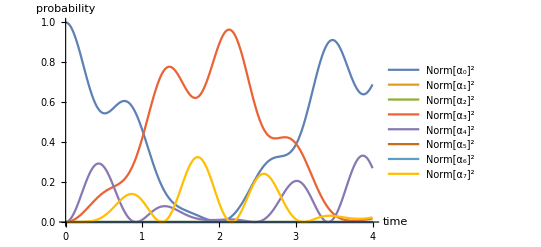

```mathematica
probs = Abs[u[t] . ψ0]^2;

Plot[probs, {t,0,4}, 
	PlotRange->All, 
	AxesLabel->{"time", "probability"},
	PlotLegends-> Table[Norm[Subscript[α, i]]^2,{i,0,2^nQb-1}]]
```

In quantum simulation, we are more often interested in the time evolution of the expectation value of some observable ⟨σ(t)⟩ = ψ(t)σ̂ ψ(t). Consider this arbitrary Pauli operator:

```mathematica
σ = Subscript[X, 0] Subscript[X, 1] Subscript[X, 2];
```

```mathematica
v = Simplify[
	Conjugate[ψ[t]] . CalcPauliExpressionMatrix[σ] . ψ[t],
	t >= 0]
```

1/20 (-1+5 Cos[4 √2 t]-4 Cos[4 √5 t])

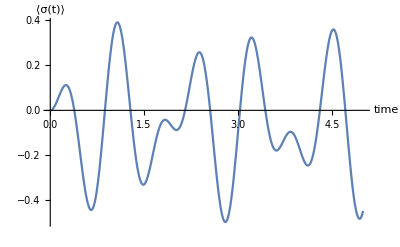

```mathematica
Plot[v, {t,0,5}, AxesLabel->{"time", "⟨σ(t)⟩"}]
```

## Numerical

Let’s switch to numerical simulation and choose a more interesting, physically-meaningful problem. We will simulate an Ising spin-ring, nominated for its potential utility in demonstrating quantum advantage, with (periodic) Hamiltonian:
        Ĥ = ∑_(i=0)^(nQb-1) (σ⃗)_i·(σ⃗)_(i+1)  +  B (Ẑ)_i +  d_i (Ẑ)_i
        
where B = 4 is the strength of a transverse magnetic field, and d_i ∈ [-d, d]

```mathematica
nQb = 7;
Clear[h]

h[d_] = Expand[
	   Sum[(4 + d  RandomReal[{-1,1}]) Subscript[Z, i], {i,0,nQb-1}] +
	 Sum[Subscript[s, i] Subscript[s, Mod[i+1,nQb]], {i,0,nQb-1}, {s,{X,Y,Z}}]]
```

X_0 X_1+X_1 X_2+X_2 X_3+X_3 X_4+X_4 X_5+X_0 X_6+X_5 X_6+Y_0 Y_1+Y_1 Y_2+Y_2 Y_3+Y_3 Y_4+Y_4 Y_5+Y_0 Y_6+Y_5 Y_6+4 Z_0+0.889235 d Z_0+4 Z_1+0.115662 d Z_1+Z_0 Z_1+4 Z_2+0.15242 d Z_2+Z_1 Z_2+4 Z_3-0.917439 d Z_3+Z_2 Z_3+4 Z_4-0.606932 d Z_4+Z_3 Z_4+4 Z_5+0.411064 d Z_5+Z_4 Z_5+4 Z_6+0.0813288 d Z_6+Z_0 Z_6+Z_5 Z_6

A quick way to confirm the ring topology of this system is to plot the connectivity of its Trotter circuit.

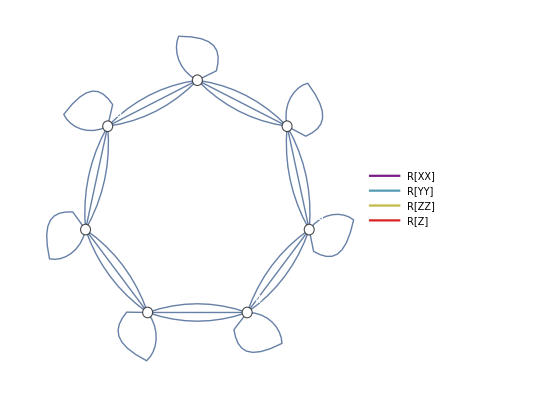

```mathematica
DrawCircuitTopology @ GetKnownCircuit["Trotter", h[1], 1,1, t]
```

The uniformly random real scalars d_i∈ [-d, d]  in  Ĥ  vary the effective magnetic field experienced by the spins. The scalar d > 0 is the strength of the disorder of the field.

```mathematica
CalcPauliStringMinEigVal @ h[1]
```

-21.6352

```mathematica
CalcPauliStringMinEigVal @ h[10]
```

-41.2231

This greatly affects the spectrum λ_j

```mathematica
vals = Transpose @ Table[
	- Eigenvalues[
		- CalcPauliExpressionMatrix @ h[d], 5,
		Method->{"Arnoldi","Criteria"->"RealPart"}],
	{d, .1, 5, .1}];
```

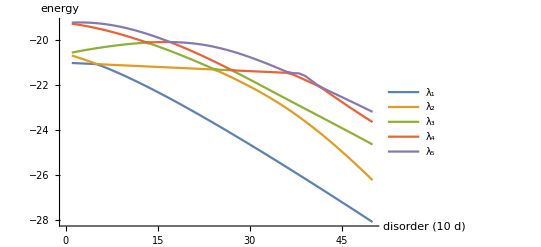

```mathematica
ListLinePlot[
	vals,
	AxesLabel-> {"disorder (10 d)", "energy"},
	PlotLegends-> Table[Subscript[λ, i],{i,5}]]
```

To simulate time evolution under Ĥ , we will make use of its Z-basis matrix representation. Here we use a Mathematica trick to save the matrix being computed for a given value of d so that repeated calls to hMatr[d] below don’t repeat the computation.

```mathematica
Clear[hMatr]
hMatr[d_] := hMatr[d] = CalcPauliExpressionMatrix @ h[d]
```

```mathematica
First @ Timing @ hMatr[.1]
```

0.03099

```mathematica
First @ Timing @ hMatr[.1]
First @ Timing @ hMatr[.1]
First @ Timing @ hMatr[.1]
```

8.×10^-6

6.×10^-6

5.×10^-6

Let’s consider an initial state whereby half of the spins are excited against the external field; this is the “Néel ordered state”.

```mathematica
inψ = CreateQureg[nQb];
ApplyCircuit[inψ, Table[Subscript[X, q],{q,0,nQb-1, 2}]];
```

```mathematica
GetQuregState[inψ, "ZBasisKets"]
```

1010101

We now numerically construct the time evolution operator in order to obtain future states.

```mathematica
trueψ = CreateQureg[nQb];

setTrueState[trueψ_, inψ_, hMatr_, t_] :=
	SetQuregMatrix[trueψ, MatrixExp[-ⅈ t hMatr] . GetQuregState[inψ]]
```

Time evolution under this Hamiltonian quickly excites the other spins:

```mathematica
setTrueState[trueψ, inψ, hMatr[.1], 0];
GetQuregState[trueψ, "ZBasisKets"]
```

1010101

```mathematica
setTrueState[trueψ, inψ, hMatr[.1], 10^-6];
GetQuregState[trueψ, "ZBasisKets"] // Chop
```

(0.-2.×10^-6 ⅈ) 0110101-(0.+2.×10^-6 ⅈ) 1001101-(0.+2.×10^-6 ⅈ) 1010011+(1.+9.09068×10^-6 ⅈ) 1010101-(0.+2.×10^-6 ⅈ) 1010110-(0.+2.×10^-6 ⅈ) 1011001-(0.+2.×10^-6 ⅈ) 1100101

```mathematica
setTrueState[trueψ, inψ, hMatr[.1],1];
GetQuregState[trueψ, "ZBasisKets"][[;;10]]
```

(-0.0233376+0.0143622 ⅈ) 0001111-(0.0870519+0.171909 ⅈ) 0010111+(0.0767504-0.0120878 ⅈ) 0011011-(0.0531524+0.103575 ⅈ) 0011101-(0.103286-0.0211168 ⅈ) 0011110-(0.120611-0.0299637 ⅈ) 0100111-(0.0736363-0.129366 ⅈ) 0101011-(0.197389-0.338313 ⅈ) 0101101+(0.167059-0.0165693 ⅈ) 0101110+(0.0198486-0.0990428 ⅈ) 0110011

In this system, we are interested in the single-site magnetisation of the spins, ⟨Z_i⟩.

```mathematica
ϕ = CreateQureg[nQb];
CalcExpecPauliString[trueψ, Subscript[Z, 0], ϕ]
```

-0.163828

Let’s check how the magnetisation of the first qubit (which started anti-aligned with the transverse magnetic field) evolves in time, for a specific choice of disorder d.

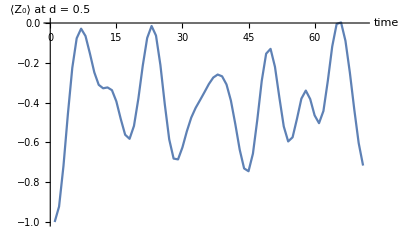

```mathematica
pureData = Table[
	setTrueState[trueψ, inψ, hMatr[.5], t];
	CalcExpecPauliString[trueψ, Subscript[Z, 0], ϕ],
	{t, 0, nQb, .1}];

ListLinePlot[pureData, AxesLabel->{"time", "⟨Z_0⟩ at d = 0.5"}]
```

Here’s how the magnetisation of all spins evolve in time, when the field has small disorder.

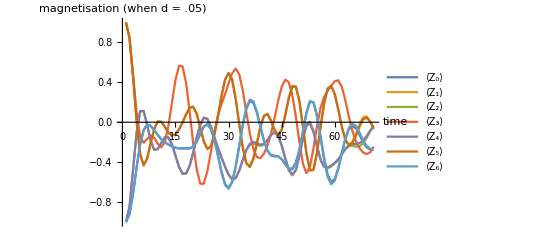

```mathematica
data = Transpose@ Table[
	setTrueState[trueψ, inψ, hMatr[.01], t];
	CalcExpecPauliString[trueψ, Subscript[Z, q], ϕ],
	{t, 0, nQb, .1},
	{q, 0, nQb-1}];

ListLinePlot[data, 
	AxesLabel->{"time", "magnetisation (when d = .05)"},
	PlotLegends-> Table[Row@{"⟨",Subscript[Z, i],"⟩"}, {i, 0,nQb-1}]]
```

We see that the strong ±1 magnetisation of our initial state is quickly thermalized, and averages around zero. As reported here, the reason that this system is interesting is because as the disorder d of the transverse magnetic field is increased, the spins take significantly longer to thermalize. A strongly disordered external field sees the spins remain localized, retaining information about their original magnetisation. Here’s the magnetisation in-time when the disorder is d = 3...

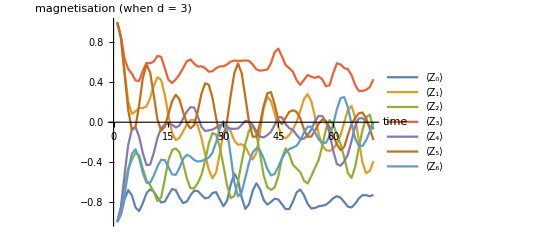

```mathematica
data = Transpose@ Table[
	setTrueState[trueψ, inψ, hMatr[5], t];
	CalcExpecPauliString[trueψ, Subscript[Z, q], ϕ],
	{t, 0, nQb, .1},
	{q, 0, nQb-1}];

ListLinePlot[data, 
	AxesLabel->{"time", "magnetisation (when d = 3)"},
	PlotLegends-> Table[Row@{"⟨",Subscript[Z, i],"⟩"}, {i, 0,nQb-1}]]
```

and when d = 10...

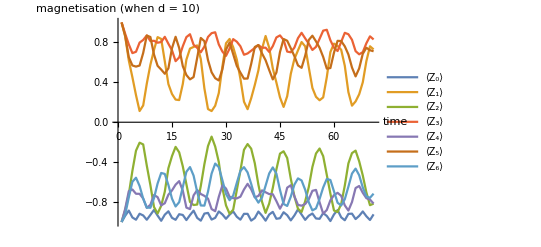

```mathematica
data = Transpose@ Table[
	setTrueState[trueψ, inψ, hMatr[10], t];
	CalcExpecPauliString[trueψ, Subscript[Z, q], ϕ],
	{t, 0, nQb, .1},
	{q, 0, nQb-1}];

ListLinePlot[data, 
	AxesLabel->{"time", "magnetisation (when d = 10)"},
	PlotLegends-> Table[Row@{"⟨",Subscript[Z, i],"⟩"}, {i, 0,nQb-1}]]
```

There is in fact a phase transition in the magnetisation occurring over d.

```mathematica
data = Transpose @ Table[
	Abs /@ Mean /@ Transpose @ Table[
	setTrueState[trueψ, inψ, hMatr[d], t];
	CalcExpecPauliString[trueψ, Subscript[Z, q], ϕ],
	{t, 0, nQb/2, .1},
	{q, 0, nQb-1}],
	{d, .01, 30, 1}];
```

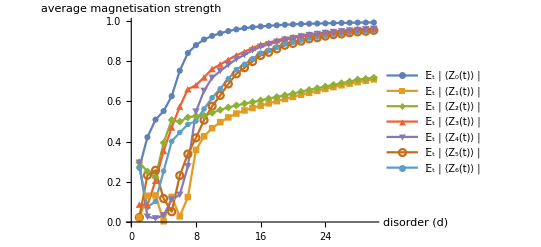

```mathematica
ListLinePlot[data, 
	AxesLabel-> {"disorder (d)", "average magnetisation strength"}, 
	PlotLegends-> Table[Row@{"𝔼_t | ⟨",Subscript[Z, i],"(t)⟩ |"}, {i, 0,nQb-1}],
	PlotMarkers->Automatic
]
```

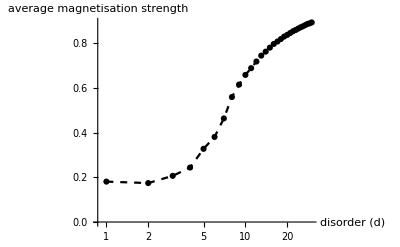

```mathematica
ListLogLinearPlot[
	Mean @ data, 
	AxesLabel-> {"disorder (d)", "average magnetisation strength"},
	Joined -> True, PlotMarkers->Automatic,
	PlotStyle->Directive[Black, Dashed]
]
```

## Trotterisation

### Pure

Let’s pretend the previous section’s spin-ring Hamiltonian was sadly too big to process by the classical numerics above, though it remains tractable to describe as a Pauli string:

```mathematica
h1 = h[1]
```

X_0 X_1+X_1 X_2+X_2 X_3+X_3 X_4+X_4 X_5+X_0 X_6+X_5 X_6+Y_0 Y_1+Y_1 Y_2+Y_2 Y_3+Y_3 Y_4+Y_4 Y_5+Y_0 Y_6+Y_5 Y_6+4.88923 Z_0+4.11566 Z_1+Z_0 Z_1+4.15242 Z_2+Z_1 Z_2+3.08256 Z_3+Z_2 Z_3+3.39307 Z_4+Z_3 Z_4+4.41106 Z_5+Z_4 Z_5+4.08133 Z_6+Z_0 Z_6+Z_5 Z_6

Suppose the Z-basis representation of Ĥ is classically computationally intractable, so we could not evaluate this:

```mathematica
h1Matr = CalcPauliExpressionMatrix[h1]
```

SparseArray[…]

Imagine that we fortunately we have a quantum computer at our disposal, with which to perform quantum simulation! The canonical method of quantumly simulating the real-time unitary dynamics of a system is to evaluate the circuit produced by Trotterising its unitary time evolution operator:
        ⅇ^(-ⅈ t Ĥ) ≈  ∏_i (Û)_i[t]

```mathematica
Clear[u]
u[t_] = GetKnownCircuit["Trotter", h1, 1, 1, t]
```

{R[2 t,X_0 X_1],R[2 t,X_1 X_2],R[2 t,X_2 X_3],R[2 t,X_3 X_4],R[2 t,X_4 X_5],R[2 t,X_0 X_6],R[2 t,X_5 X_6],R[2 t,Y_0 Y_1],R[2 t,Y_1 Y_2],R[2 t,Y_2 Y_3],R[2 t,Y_3 Y_4],R[2 t,Y_4 Y_5],R[2 t,Y_0 Y_6],R[2 t,Y_5 Y_6],R[9.77847 t,Z_0],R[8.23132 t,Z_1],R[2 t,Z_0 Z_1],R[8.30484 t,Z_2],R[2 t,Z_1 Z_2],R[6.16512 t,Z_3],R[2 t,Z_2 Z_3],R[6.78614 t,Z_4],R[2 t,Z_3 Z_4],R[8.82213 t,Z_5],R[2 t,Z_4 Z_5],R[8.16266 t,Z_6],R[2 t,Z_0 Z_6],R[2 t,Z_5 Z_6]}

This is a circuit with gate parameters dependent upon the coefficients of our Hamiltonian, and the target simulation time t.

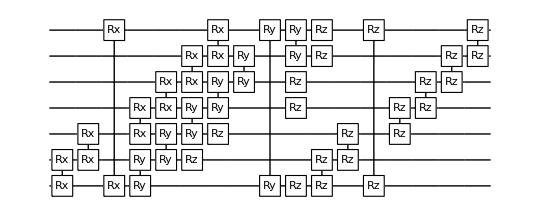

```mathematica
DrawCircuit @ u[t]
```

If necessary, we could recompile this circuit into the native operations of our hardware...

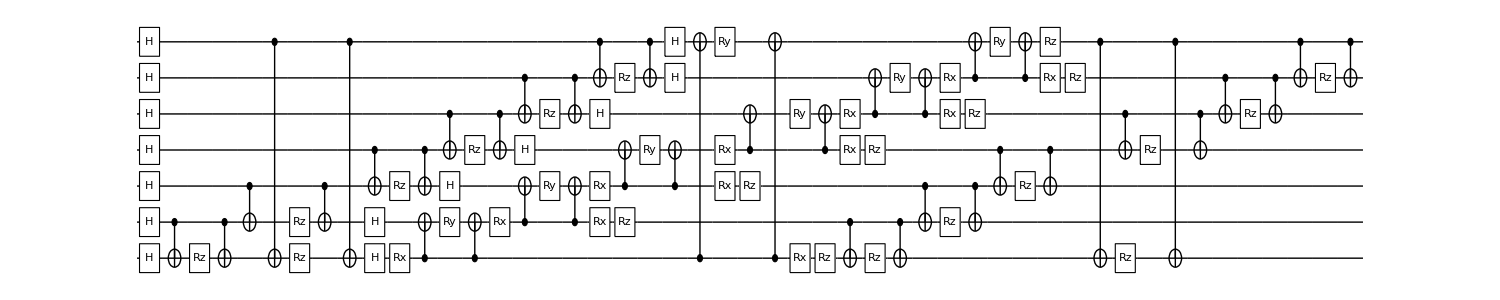

```mathematica
v = SimplifyCircuit @ RecompileCircuit[u[t], "SingleQubitAndCNOT"];
DrawCircuit[v]
```

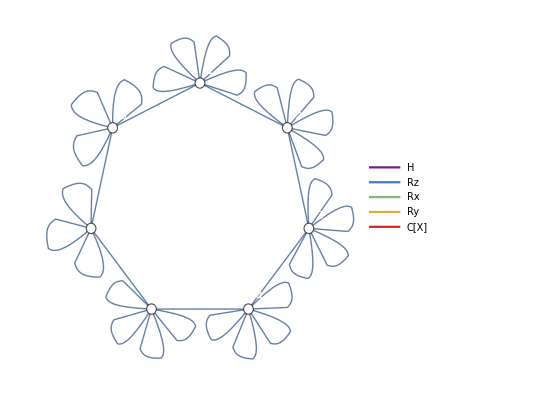

```mathematica
DrawCircuitTopology @ v
```

but for convenience, let’s assume our hardware can perform the original two-qubit Pauli gadgets. The Trotter circuit Û , applied to the initial state ψ(0), produces a direct approximation to the state ψ(t) = ⅇ^(-ⅈ t Ĥ)ψ(0)

```mathematica
ψ = CreateQureg[nQb];
CloneQureg[ψ, inψ];
GetQuregState[ψ, "ZBasisKets"]
```

1010101

```mathematica
τ = 0.1;
ApplyCircuit[ψ, u[τ]];
setTrueState[trueψ, inψ, h1Matr, τ];

CalcFidelity[ψ, trueψ]
```

0.992173

An experimentalist can ergo apply circuit Û(t), with rotations informed by the desired simulation time t, and thereafter measure their observable of interest, like the spin-ring magnetisation.

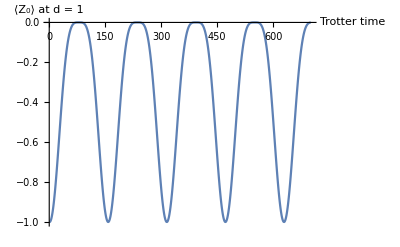

```mathematica
data = Table[
	CloneQureg[ψ, inψ];
	ApplyCircuit[ψ, u[t]];
	CalcExpecPauliString[ψ, Subscript[Z, 0], ϕ],
	{t, 0, nQb, .01}];

ListLinePlot[data, AxesLabel->{"Trotter time", "⟨Z_0⟩ at d = 1"}]
```

This doesn’t look how we expected - it is suspiciously periodic (as the Trotter circuit is as a function of t), whereas we earlier witnessed thermalisation. Indeed the fidelity is imperfect - Trotterisation can only approximate the evolution when the Hamiltonian contains non-commuting terms.

```mathematica
τ = 0.3;
ApplyCircuit[CloneQureg[ψ, inψ], u[τ]];
setTrueState[trueψ, inψ, h1Matr, τ];

CalcFidelity[ψ, trueψ]
```

0.812077

The fidelity (| ψ(0)ⅇ^(ⅈ t Ĥ) Û(t)ψ(0)|)^2 drops quickly with increasing t.

```mathematica
Bra[ψ]
```

32

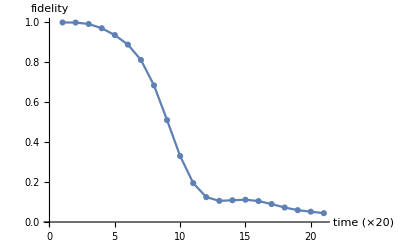

```mathematica
fid = Table[
	ApplyCircuit[CloneQureg[ψ, inψ], u[t]];
	setTrueState[trueψ, inψ, h1Matr, t];
	CalcFidelity[ψ, trueψ],
	{t,0, 1, .05}];

ListLinePlot[fid,
	AxesLabel->{"time (×20)", "fidelity"},
	PlotMarkers->Automatic
]
```

We can improve the fidelity by using more Trotter repetitions, or using a higher order method.

```mathematica
order = 4;
reps = 3;
u[t_] = GetKnownCircuit["Trotter", h1,order, reps, t]
```

{R[t/(3 (4-2^(2/3))),X_0 X_1],R[t/(3 (4-2^(2/3))),X_1 X_2],R[t/(3 (4-2^(2/3))),X_2 X_3],R[t/(3 (4-2^(2/3))),X_3 X_4],818,R[t/(3 (4-2^(2/3))),X_2 X_3],R[t/(3 (4-2^(2/3))),X_1 X_2],R[t/(3 (4-2^(2/3))),X_0 X_1]}
 |  |  |  |

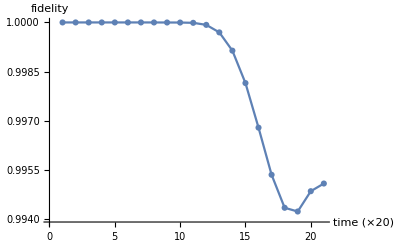

```mathematica
fid = Table[
	ApplyCircuit[CloneQureg[ψ, inψ], u[t]];
	setTrueState[trueψ, inψ, h1Matr, t];
	CalcFidelity[ψ, trueψ],
	{t,0, 1, .05}];

ListLinePlot[fid,
	AxesLabel->{"time (×20)", "fidelity"},
	PlotMarkers->Automatic
]
```

Of course, this means increasing the number of gates in the circuit.

```mathematica
Length @ GetKnownCircuit["Trotter", h1,4, 1, t]
```

275

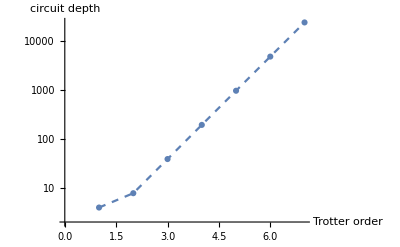

```mathematica
cost = Table[
	Length @ GetKnownCircuit["Trotter", h1,order, 1, t] / nQb,
	{order, {1,2,4,6,8,10, 12}}];

ListLogPlot[cost,
	AxesLabel-> {"Trotter order", "circuit depth"},
	Joined -> True, PlotMarkers->Automatic, 
	PlotStyle -> Directive[Dashed]
]
```

Let’s simulate to fixed time t = nQb/2, and record the costs and performance of using Trotter circuits of different order and repetitions.

```mathematica
τ = nQb / 2;
setTrueState[trueψ, inψ, h1Matr, τ];

data = Table[
	u = GetKnownCircuit["Trotter", h1, order, reps, N@τ];
	ApplyCircuit[CloneQureg[ψ, inψ], u];
	{Length[u], CalcFidelity[ψ, trueψ]},
	{order, {1,2,4,6,8}},
	{reps, 1, Floor[100/order]}];
```

We can see that higher-order Trotter quickly becomes expensive:

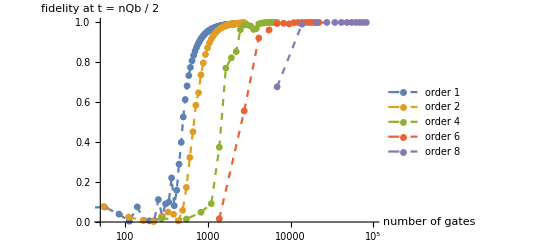

```mathematica
ListLogLinearPlot[data,
	AxesLabel-> {"number of gates", "fidelity at t = nQb / 2"},
	Joined -> True, PlotRange-> {{.5 10^2,10^5}, All},
	PlotStyle->Dashed, PlotMarkers->{"●", 7},
	Ticks -> {Table[{10^i,("10")^i},{i,1,5}], Automatic},
	PlotLegends-> Table["order " <> ToString[i], {i,{1,2,4,6,8}}]
]
```

yet it is our only hope if we wish to simulate far into the future!

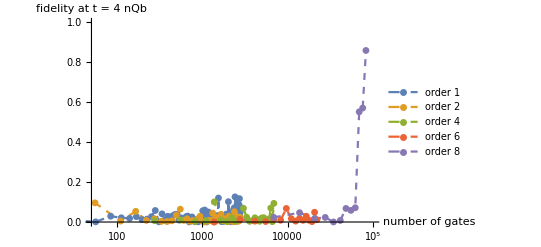

```mathematica
τ = 4 nQb;
setTrueState[trueψ, inψ, h1Matr, τ];

data = Table[
	u = GetKnownCircuit["Trotter", h1, order, reps, N@τ];
	ApplyCircuit[CloneQureg[ψ, inψ], u];
	{Length[u], CalcFidelity[ψ, trueψ]},
	{order, {1,2,4,6,8}},
	{reps, 1, Floor[100/order]}];

ListLogLinearPlot[data,
	AxesLabel-> {"number of gates", "fidelity at t = 4 nQb"},
	Joined -> True, PlotRange-> {{.5 10^2,10^5}, {0,1}},
	PlotStyle->Dashed, PlotMarkers->{"●", 7},
	Ticks -> {Table[{10^i,("10")^i},{i,1,5}], Automatic},
	PlotLegends-> Table["order " <> ToString[i], {i,{1,2,4,6,8}}]
]
```

### Noisy

There is yet another problem - what happens if our quantum hardware is imperfect and susceptible to decoherence? Let’s now assume that parameter-dependent dephasing noise of probability ξ|θ| follows every Rz[θ] gate, and fixed two-qubit depolarising noise of strength ξ follows every two-qubit Pauli gadget.

```mathematica
noisify[u_, ξ_] := u /. {
	g:R[θ_,Subscript[Z, t_]]:>Sequence[g,Subscript[Deph, t][Abs[θ] ξ]],
	g:R[θ_,Verbatim[Times][Subscript[_, t1_],Subscript[_, t2_]] ]:>Sequence[g,Subscript[Depol, t1,t2][ξ]]}
```

Attempting to perform the first-order single-repetition unitary Trotter circuit...

```mathematica
τ = 0.1;
u = GetKnownCircuit["Trotter", h1, 1, 1, τ];
DrawCircuit[u]
```

-Graphics-

would instead invoke the channel:

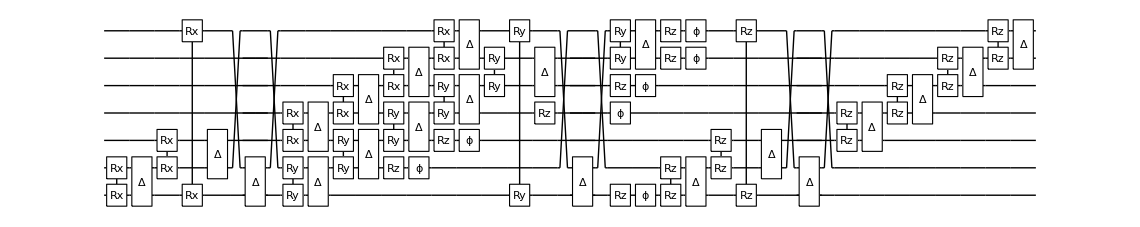

```mathematica
DrawCircuit @ noisify[u, ξ]
```

Simulating this channel will require we switch our quantum registers to be density matrices.

```mathematica
ρ= CreateDensityQureg[nQb];
InitPureState[ρ, inψ];
```

```mathematica
ApplyCircuit[ρ, noisify[u, 10^-3]];
CalcPurity[ρ]
```

0.953016

The decoherence (physical error) worsens our fidelity, compounding the existing inaccuracy of our Trotter truncation (algorithmic error)

```mathematica
setTrueState[trueψ, inψ, h1Matr, τ];

InitPureState[ρ, inψ];
ApplyCircuit[ρ, noisify[u, 10^-2]];
CalcFidelity[ρ, trueψ]
```

0.824697

Here’s first-order single-repetition Trotter simulation succumbing to increasing decoherence.

```mathematica
noise = Range[0, 10^-2, 10^-3];
data = Transpose @ Table[
	InitPureState[ρ, inψ];
	ApplyCircuit[ρ, noisify[u, ξ]];
	{CalcFidelity[ρ, trueψ], CalcPurity[ρ]},
	{ξ, noise}];
```

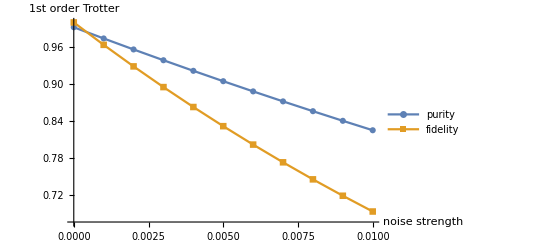

```mathematica
ListLinePlot[
	Transpose[{noise, #}]& /@ data,
	AxesLabel-> {"noise strength", "1st order Trotter"},
	PlotLegends -> {"purity", "fidelity"},
	PlotMarkers->Automatic
]
```

While the algorithmic Trotter error worsens for increasing t, the physical error of decoherence worsens the fidelity at all times. Even a measly t=1 simulation is quickly ruined!

```mathematica
Clear[u];
u[t_] =  GetKnownCircuit["Trotter", h1, 4, 1, t];
ch[t_, ξ_] = noisify[u[t], ξ];
```

```mathematica
time = Range[0,1,0.05];
noise =  {0,10^-4,10^-3,2 10^-3, 5 10^-3,10^-2};
fid = Transpose @  Table[
	setTrueState[trueψ, inψ, h1Matr, t];
	ApplyCircuit[InitPureState[ρ, inψ], ch[t, ξ]];
	CalcFidelity[ρ, trueψ],
	{t,time},
	{ξ,noise}];
```

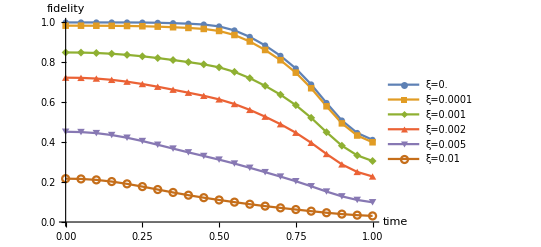

```mathematica
ListLinePlot[
	Transpose[{time, #}]& /@ fid,
	AxesLabel->{"time", "fidelity"},
	PlotLegends-> Table["ξ="<>ToString[N@ξ],{ξ,noise}],
	PlotMarkers->Automatic
]
```

Let’s repeat our earlier resource-aware simulations of time t = nQb/2 using increasing Trotter orders and repetitions, but this time incorporating a modest physical error rate of ξ = 10^-4.

```mathematica
τ = nQb / 2;
ξ = 10^-4;
setTrueState[trueψ, inψ, h1Matr, τ];

data = Table[
	u = GetKnownCircuit["Trotter", h1, order, reps, N@τ];
	ApplyCircuit[InitPureState[ρ, inψ], noisify[u,ξ]];
	{Length[u], CalcFidelity[ρ, trueψ]},
	{order, {1,2,4,6,8}},
	{reps, 1, Floor[100/order]}];
```

This reveals increasing the Trotter repetitions and order can actually worsen performance, because the additional gates introduce more opportunities for physical error:

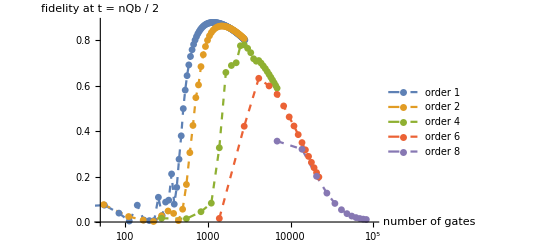

```mathematica
ListLogLinearPlot[data,
	AxesLabel-> {"number of gates", "fidelity at t = nQb / 2"},
	Joined -> True, PlotRange-> {{.5 10^2,10^5}, All},
	PlotStyle->Dashed, PlotMarkers->{"●", 7},
	Ticks -> {Table[{10^i,("10")^i},{i,1,5}], Automatic},
	PlotLegends-> Table["order " <> ToString[i], {i,{1,2,4,6,8}}]
]
```

This is why Trotterisation is believed to be incompatible with near-future noisy quantum hardware. It prescribes deep circuits leveraging precise interference effects, which are easily damaged by noise and the imperfections of near-future quantum computers.

How would the experimentalist fair attempting to use this hardware to study the dynamics of magnetisation in our spin-ring system?

```mathematica
μ = CreateDensityQureg[nQb];
```

```mathematica
data = Table[
	u = GetKnownCircuit["Trotter", h1, 4, 1, t];
	ApplyCircuit[InitPureState[ρ, inψ], noisify[u,10^-4]];
	CalcExpecPauliString[ρ, Subscript[Z, 0], μ],
	{t, 0, nQb, .1}];
```

Well at least it more closely resembles thermalization! .af\_(ツ)_/.af

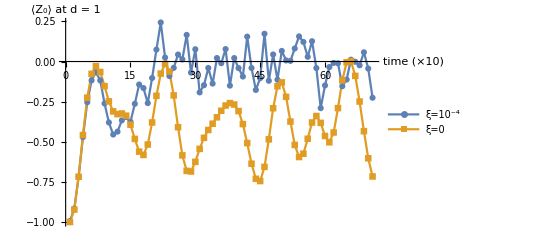

```mathematica
ListLinePlot[
	{data, pureData},
	AxesLabel->{"time (×10)", "⟨Z_0⟩ at d = 1"}, 
	PlotMarkers->Automatic,
	PlotLegends->{"ξ=10^-4", "ξ=0"}]
```